```mathematica
f[x]:= (x^5-2x^2+3x+4)/(x^5-2x-1)
```

```mathematica
ReplaceAll[f[x], x ->{1,2,3,4}]
```

{-3,34/27,119/118,144/145}

```mathematica
Table[f[x], {x, 1, 10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
sez={10,20,30,40,50,60,70}
```

{10,20,30,40,50,60,70}

```mathematica
sez[[{1,2,3}]]
```

{10,20,30}

```mathematica
sez[[{6,7}]]
```

{60,70}

```mathematica
sez[[{2,3,4}]]
```

{20,30,40}

```mathematica
sez[[{2,3,5}]]
```

{20,30,50}

```mathematica
Drop[sez, {4,5}]
```

{10,20,30,60,70}

```mathematica
sez={x^6,x^2,a}
```

{x^6,x^2,a}

```mathematica
ReplaceAll[sez, x->3]
```

{729,9,a}

```mathematica
ReplaceAll[sez, x->x^2]
```

{x^12,x^4,a}

```mathematica
ReplaceAll[sez, x^2->x]
```

{x^6,x,a}

```mathematica
ReplaceAll[sez, x->{1,2,3}]
```

{{1,64,729},{1,4,9},a}

```mathematica
ReplaceAll[{x^6,x^2,a},x->{1,2,3}]
```

{{1,64,729},{1,4,9},a}

```mathematica
ReplaceRepeated[sez, {x->3, a->x}]
```

{729,9,3}

```mathematica
f[x]:= x^5 + 4x^3-9
D[f[x], x] /.x->{1,5}
```

{17,3425}

```mathematica
f[x]:=E^(x^(1/4))
```

```mathematica
D[f[x],x] /. x->{1,2}
```

{ⅇ/4,(ⅇ^(2^(1/4)))/(4 2^(3/4))}

```mathematica
f[x]:= Abs [x+1]
```

```mathematica
FullSimplify[ D[f[x],x]/. x->{1,-1}]
```

Abs'[{2,0}]

```mathematica
f[x]:=a*x^2+3*b
D[f[x],x]/. x->{1,2}
```

{2 a,4 a}

```mathematica
Clear[f[x]]
```

Clear::ssym: f[x] is not a symbol or a string.

```mathematica
f[x_]:=x^3Log[4x+5]
```

```mathematica
Plot[f[x],{x,1,10}]
```

-Graphics-

```mathematica
Limit [(x^3-4x^2+2x+4)/(x^5-9x-14), x->2]
```

-2/71

```mathematica
Limit[ArcTan[7x]/ArcSin[8x],x->0]
```

7/8

```mathematica
Limit[(x^2-25)*Cot[π*x], x->5]
```

10/π

```mathematica
Limit[(1+Cos[x])/(2*√(π*x)-π-x), x->π]
```

-2 π

```mathematica
Limit
```

```mathematica
f[x_]:= (x^2 - 1)/(x^2 - 4)
```

Replace::reps: {3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Naloga 8
```

```mathematica
izraz = x^4 + x^3 - x
```

-x+x^3+x^4

```mathematica
resitve = x/.Solve[izraz == 0 && x > 0, x]
Power [resitve, 2] // N
```

{Root0.755Root[-1+#1^2+#1^3&,1]0.7548776662466927}

{0.56984}

```mathematica
Naloga 9

enacba1= 3x^2 - 5y^2 == 5
```

3 x^2-5 y^2==5

```mathematica
enacba2 = 2x^2 + 3y^2 == 59
```

2 x^2+3 y^2==59

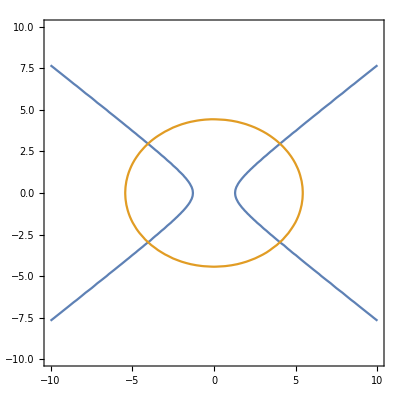

```mathematica
ContourPlot[{3x^2 - 5y^2 == 5, 2x^2 + 3y^2 == 59}, {x, -10, 10}, {y, -10, 10}]
```

```mathematica
Solve[{enacba1, enacba2}, {x,y}]
```

{{x→-√(310/19),y→-√(167/19)},{x→-√(310/19),y→√(167/19)},{x→√(310/19),y→-√(167/19)},{x→√(310/19),y→√(167/19)}}

```mathematica
resitev = Solve[enacba1 && enacba2 && x>0 && y>0, {x.y}]
x0 = x /. resitev[[1]]
y0 = y/. resitev[[1]]
```

{}

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x/.{}⟦1⟧

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

y/.{}⟦1⟧